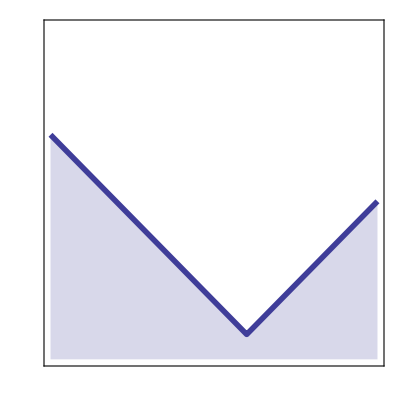

```mathematica
Linear = Plot[3+Abs[x-4],{x,-20,20},Filling->Axis,PlotRange->{0,40},Axes->{True,False},Ticks->False,PlotStyle->{Thickness[.01]},Frame->True,FrameTicks->False,PlotRangePadding->0,FrameStyle->Directive[Thickness[0.005]],AspectRatio->1]
```

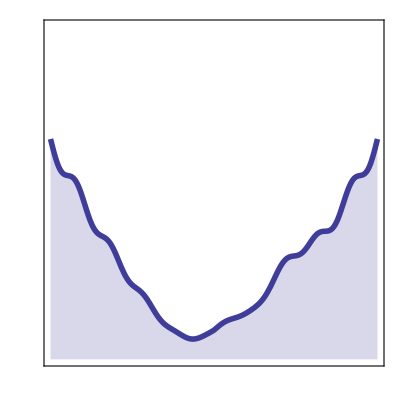

```mathematica
Convex = Plot[0Exp[-(x+6)^2/40]+500Exp[-(x-2)^2/30]+500Exp[-(x-13)^2/30]+(Cos[x]+20)Abs[x Sqrt[Abs[x]]],{x,-30,30},Filling->Axis,PlotRange->{0,5000},Axes->{True,False},Ticks->False,PlotStyle->{Thickness[.01]},Frame->True,FrameTicks->False,PlotRangePadding->0,FrameStyle->Directive[Thickness[0.005]],AspectRatio->1]
```

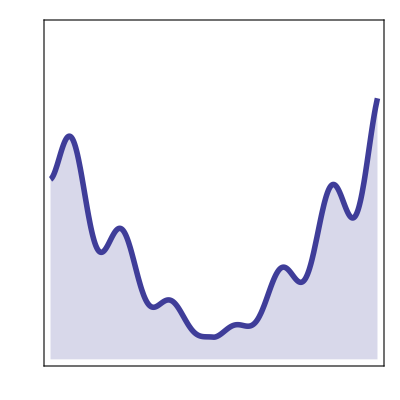

```mathematica
Nonconvex = Plot[10+Abs[x (Sin[x]+Sqrt[Abs[x]])],{x,-20,20},PlotRange->{0,150},Filling->Axis,Axes->{True,False},Ticks->False,PlotStyle->{Thickness[.01]},Frame->True,FrameTicks->False,PlotRangePadding->0,FrameStyle->Directive[Thickness[0.005]],AspectRatio->1]
```

```mathematica
SetDirectory["/home/filipe/Documents/PhD-Thesis/"];
```

```mathematica
Export["LinearObjectiveFunction.pdf",Linear];
```

```mathematica
Export["ConvexObjectiveFunction.pdf",Convex];
```

```mathematica
Export["NonconvexObjectiveFunction.pdf",Nonconvex];
```